# Falling of pen on table(curve)

```mathematica
Clear["Global`*"]
```

```mathematica
(* functions *)
c1hs[x_,scale_]:=(Tanh[x/scale]+1)/2
tgv[f_,x_,t_]:=Normalize[{1,D[f[p,q],p]/.{p->x,q->t}}]
nmv[f_,x_,t_]:=Normalize[RotationMatrix[Pi/2].{1,D[f[p,q],p]/.{p->x,q->t}}]
```

```mathematica
Tend=5;
vCux=-0.01;
vCuy=0.01;
vCur=0.1;
m=0.2;(* pen mass *)
R=0.005;(* pen radius *)
h=0.1;(* pen length *)
scalt=0.00001;(* detect contact activation time *)
data={(*gravity*)g->10,
(* inertia moments*)
Jzz->1/2 m R^2,Jxx-> m/4 ( R^2+h^2/3),Jyy-> m/4 ( R^2+h^2/3),
(* contact and sliding stiffness*)
kz->5 10^4,μx->.05 };

(* movement of the curve *)
r[t_]:=RotationTransform[vCur t,{0,0}]
curve[x_,t_]:=(r[t])[{x,1.7h/3Exp[-(x+vCux t)]+vCuy t}][[2]]
```

```mathematica
(* inertia center & front and rear ends of pen *)
xC[t_]:={xCx[t],xCz[t]}
xSf[t_]:=xC[t]+1/(2Sqrt[2]) RotationMatrix[θ[t]].{0,-1.4h}
xSr[t_]:=xC[t]+1/(2Sqrt[2]) RotationMatrix[θ[t]].{0,1.4h}
```

```mathematica
(* velocity in the tangent direction of the curve *)
vSftg[t_]:=xSf'[t].tgv[curve,xSf[t][[1]],t]
vSrtg[t_]:=xSr'[t].tgv[curve,xSr[t][[1]],t]

(* depth in the curve table *)
dSf[t_]:={0,curve[xSf[t][[1]],t]-xSf[t][[2]]}.nmv[curve,xSf[t][[1]],t]
dSr[t_]:={0,curve[xSr[t][[1]],t]-xSr[t][[2]]}.nmv[curve,xSr[t][[1]],t]
```

```mathematica
(* contact forces against @z=0 at both ends of pen *)
(* c1hs[...] is for purpose of determining whether there's contact forces *)
fSf[t_]:=-μx c1hs[curve[xSf[t][[1]],t]-xSf[t][[2]],scalt] vSftg[t] tgv[curve,xSf[t][[1]],t]+kz c1hs[curve[xSf[t][[1]],t]-xSf[t][[2]],scalt]dSf[t]nmv[curve,xSf[t][[1]],t];
fSr[t_]:=-μx c1hs[curve[xSr[t][[1]],t]-xSr[t][[2]],scalt]vSrtg[t]tgv[curve,xSr[t][[1]],t]+kz c1hs[curve[xSr[t][[1]],t]-xSr[t][[2]],scalt]dSr[t]nmv[curve,xSr[t][[1]],t];
```

```mathematica
eqNewton=Thread[m xC''[t]+0.01 m xC'[t]==-m g {0,1}+fSf[t]+fSr[t]];
eqEuler= Jxx θ''[t]+0.01 Jxx θ'[t]==Det[{xSf[t]-xC[t],fSf[t]}]+Det[{xSr[t]-xC[t],fSr[t]}];
```

```mathematica
eqinit={xCx[0]==0,xCz[0]== 1.5h,xCx'[0]==0.1,xCz'[0]==0,θ[0]==Pi/4,θ'[0]==-Pi/30};
```

```mathematica
solpen=NDSolve[Flatten[{eqNewton,eqEuler,eqinit}]/.data,{xCx,xCz,θ},{t,0,Tend},MaxStepFraction->1/10000,MaxStepSize->0.001][[1]]
```

{xCx→InterpolatingFunction[…],xCz→InterpolatingFunction[…],θ→InterpolatingFunction[…]}

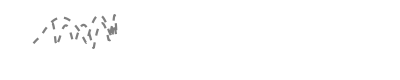

```mathematica
gC=ParametricPlot[xC[t]/.solpen,{t,0,Tend}, Axes->False,PlotStyle->{Gray,Dashed},PlotRange->{{-0.5h,10h},{-0.1h,2h}}]
```

```mathematica
Animate[Show[gC,Plot[curve[x,t],{x,-0.5h,10h},PlotStyle->Gray],Graphics[{{PointSize[Large],Point[xC[t]/.solpen]},{Thick,Blue,Line[{(xSr[t])/.solpen,(xSf[t])/.solpen}]}},PlotRange->{{-0.5h,10h},{-0.1h,2h}}]],{t,0,Tend,0.0001},AnimationRunning->False]
```